```mathematica
fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals, FullSimplify@x]
myFormatConvertToNegativePowers = StandardForm[#/.Power[expr_, r_?Negative] :> Superscript[expr,r] ]&;

CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);

KPE=0.4;
KPDUST = 50;       (* dust kappa *)


SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7/μm/.μm->1.;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;

MBH=10^7 Msol;

MP=1.672661 10^-24;

SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;
KM=10^5;


rulzGlob = {α->0.1, ϵ->0.1, η->0.1,  M->MBH, μ->1};


rulForConst={J->1, m->1,Rg->RGAS, σ->SGB, a->ARAD, G->Gr,c->CL, a->ARAD};


CalculateMdotNumber[rul_, excess_] := Module[{res},
	res =excess* μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rul];

(*Dust opacity interpolation formuas*)
TSUB =1500;
```

```mathematica
SGB
```

0.0000566956

# Dust sublimation surface

```mathematica
ClearAll[GiveZTsurf,TsubSurf]

GiveZTsurf[x_,par_]:=Module[{Ts=TSUB,KP1=KPE,τ=2/3,GM=Gr par[Mbh],Fs,Fn,f=1,eqT,res},

Fn= f par[Gam]CL/KP1;

(*Echo[Fn];*)

Fs= 9/(32π)(2/3+τ) par[Mdt];

eqT=(GM/SGB(Fs + Fn (z^2+x^2)^(1/2))(z^2+x^2)^(-3/2))^(1/4);
(*Echo[eqT];*)

If[Length[res=NSolve[eqT==Ts &&z>0.,z,Reals]]>0,
(res//Flatten)⟦1,2⟧]
]


Module[{Rout=0.5PC,par},

par=<|Mbh->MBH, Mdt->0.2MsolYr, Gam->0., α->0.1, OmegaSlope->1.5,R0->0.001PC,xmin->0.0051, xmax->0.3,zmin->0., zmax->0.01, Nx1-> 50|>;

X1=0.01;

GiveZTsurf[PC X1,par]/(X1 PC)

(*ContourPlot[TsubSurf[PC x,PC z,par](*==TSUB*),{x, par[xmin],par[xmax]}, {z, par[zmin],par[zmax]}]
*)
]
```

3.24078×10^-17 Null

### Variant I

```mathematica
ClearAll[F,f,g,d,r,eqF,Subscript[A, 1],x,y,z,i1,t];

g[t_]:=Exp[-0.1/Abs[Sin[t]]];

(*g[t_]:=1;*)

i1=0;

d[t_]:=Cos[t](1+i1*2Cos[t]);

r=(x^2+z^2)^(1/2);


eqF=d[t]g[t]-r^2 Subscript[A, 1];

eqF=eqF/.{Cos[t]->z/r,Sin[t]->x/r,Csc[t]->r/x};

Subscript[A, 1]=Module[{GM,Γ,A1,T0=1500,R0},
Γ=0.1;
R0=PC;
GM=10^7 Msol Gr;

R0=(GM/KPE 1/ARAD)^(1/2)T0^-2;
A1=KPE/GM ARAD T0^4/Γ R0^2;
Print["R0 = ", R0"cm"," = ", R0/PC," PC"];
Print["A1=",A1];
A1
];


F[x_,z_]:= Numerator[Together[eqF]]

F[x,z];

ContourPlot[F[x,z],{x, 0.0,0.3}, {z, 0.,8}
```

R0 = 2.94289×10^17 cm = 0.0953725 PC

A1=10.

## Var 2 : Effective radiation temperature

ClearAll::ssym: A_1 is not a symbol or a string.

ClearAll::ssym: τ_0 is not a symbol or a string.

ClearAll::ssym: Γ_0 is not a symbol or a string.

General::stop: Further output of ClearAll::ssym will be suppressed during this calculation.

(20. z (1+(2 z)/(√(x^2+z^2))))/(√(x^2+z^2))

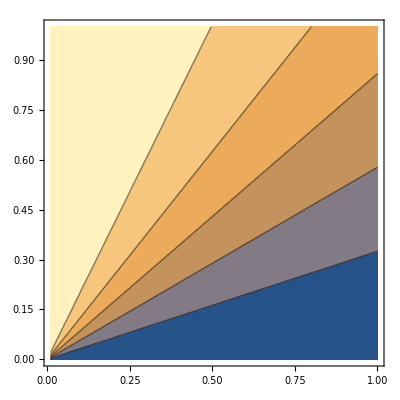

R0 = 2.94289×10^17 cm = 0.0953725 PC

B1=843.512

(843.512 z (1+(2 z)/(√(x^2+z^2))))/((x^2+z^2)^(3/2))

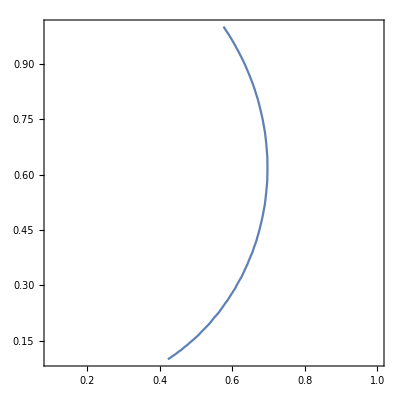

```mathematica
ClearAll[F,f,g,d,r,eqF,Subscript[A, 1],x,y,z,i1,t,Subscript[τ, 0],Subscript[Γ, 0],Gam0,eqCritGam];
rout = 1;

Gam0 = 0.1;

Subscript[τ, 0]=1;

g[t_]:=Exp[-Subscript[τ, 0]Csc[t]];

(*g[t_]:=1/(1+Subscript[τ, 0] Csc[t]);
*)
g[t_]:=1;

i1=1;

d[t_]:=Cos[t](1+i1  2Cos[t]); 


r=(x^2+z^2)^(1/2);

rul1 = {Cos[t]->z/r,Sin[t]->x/r,Csc[t]->r/x};

Subscript[κ, 2] =200;

eqCritGam= Gam0 Subscript[κ, 2] d[t]g[t]/.rul1

FunCritGam[x_,z_]:=eqCritGam;

ContourPlot[FunCritGam[x,z],{x, 0.01,rout}, {z, 0.,rout}]

eqF=d[t] g[t]/r^2 Subscript[B, 1];
eqF=eqF/.rul1;



Subscript[B, 1]=Module[{GM,Γ,B1,T0=1500,R0},
Γ=Gam0;
R0=PC;
GM=10^7 Msol Gr;
R0=(GM/KPE 1/ARAD)^(1/2)T0^-2;
B1=(KPE/GM ARAD 1/Γ R0^2)^(-1/4);
Print["R0 = ", R0"cm"," = ", R0/PC," PC"];
Print["B1=",B1];
B1
];


F[x_,z_]:= eqF;

F[x,z]

ContourPlot[F[x,z]==1500,{x, 0.1,rout}, {z, 0.1,rout}]
```

```mathematica
AngFunc= {Cos[t],Cos[t](1+2Cos[t])}
```

```mathematica
Simplify[
Grad[F[x,z], {x,z}]/.rul1, r>0
]
```

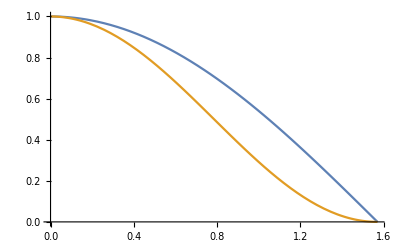

```mathematica
Plot[{Cos[t](*, Cos[t](1+2Cos[t])*),Cos[t]^2},{t,0,Pi/2}]
```

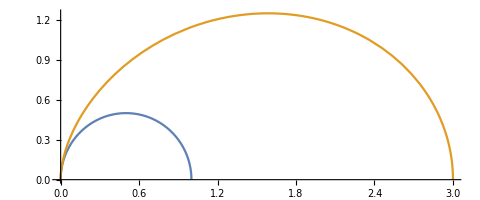

```mathematica
PolarPlot[{Cos[t], Cos[t](1+2Cos[t])},{t,0,Pi/2}]
```

## Normal and Tangent Vectors

```mathematica
F[x_,z_]:=Subscript[A, 1](x^2+z^2)^(3/2)-z
Simplify[
Grad[F[x,z], {x,z}]/.rul1, r>0
]
```

{3 r^2 Sin[t] A_1,-1+3 r^2 Cos[t] A_1}

```mathematica
F[x_,z_]:=Subscript[A, 1](x^2+z^2)^(3/2)-z

(*F[x_,z_]:=-2 z^2-z √(x^2+z^2)+(x^2+z^2)^2 Subscript[A, 1]*)

rul1 = {x->r Sin[t],z->r Cos[t]}

Nvec = {D[F[x,z], x], D[F[x,z], z]}/.rul1;
Nvec = Simplify[Nvec/(√(Nvec.Nvec)),r>0]
(*test*)
Nvec.Nvec//Simplify

Fvec = {1, (-D[F[x,z], x])/D[F[x,z], z]}//Simplify
```

{x→r Sin[t],z→r Cos[t]}

{(3 r^2 Sin[t] A_1)/(√(1-6 r^2 Cos[t] A_1+9 r^4 A_1^2)),(-1+3 r^2 Cos[t] A_1)/(√(1-6 r^2 Cos[t] A_1+9 r^4 A_1^2))}

1

{1,(3 x √(x^2+z^2) A_1)/(1-3 z √(x^2+z^2) A_1)}

```mathematica
Fvec = {1, (-D[F[x,z], x])/D[F[x,z], z]}//Simplify
```

{(3 r^2 Sin[t] A_1)/(√(1-6 r^2 Cos[t] A_1+9 r^4 A_1^2)),(-1+3 r^2 Cos[t] A_1)/(√(1-6 r^2 Cos[t] A_1+9 r^4 A_1^2))}

1

```mathematica
Norm[Nvec, A->{x>0,z>0}]//Simplify
```

```mathematica
√(9 (x √(x^2+z^2) Subscript[A, 1])^2+(1-3 z √(x^2+z^2) Subscript[A, 1])^2)/.x->r Sin[t]/.z->r Cos[t]//Simplify
```

```mathematica
√(1-6 r r Cos[t] Subscript[A, 1]+9 r^4 Subscript[A, 1]^2)//FullSimplify
```

√(1-6 r^2 Cos[t] A_1+9 r^4 A_1^2)

```mathematica
Fvec = {1, (-D[F[x,z], x])/D[F[x,z], z]}//Simplify
```

{1,(3 x √(x^2+z^2) A_1)/(1-3 z √(x^2+z^2) A_1)}

```mathematica
Fvec/.{√(x^2+z^2)->r}/.x->r sint/.z->r cost//Simplify
```

{1,(3 r^2 sint A_1)/(1-3 cost r^2 A_1)}

```mathematica
Fvec.Nvec
```

3 x √(x^2+z^2) A_1+(3 x √(x^2+z^2) A_1 (-1+3 z √(x^2+z^2) A_1))/(1-3 z √(x^2+z^2) A_1)